# Wikipedia Page Analysis

### Import raw data form wikipedia

```mathematica
url="http://en.wikipedia.org/w/api.php?action=query&prop=revisions&titles=Mathematica&rvprop=user|timestamp&rvlimit=500&redirects$rvuser&format=xml";
```

```mathematica
xml=Import[url,"XML"];
```

```mathematica
rawdata=Cases[xml,XMLElement["rev",w_,_]:>w,Infinity];
```

```mathematica
data={"user","timestamp"}/.rawdata;
```

```mathematica
timestamp=data[[All,2]];
```

```mathematica
dates=DateList[{#,{"Year","-","Month","-","Day","T","Hour",":","Minute",":","Second","Z"}}][[1;;3]]&/@timestamp;
```

```mathematica
revhist=Tally[dates];
```

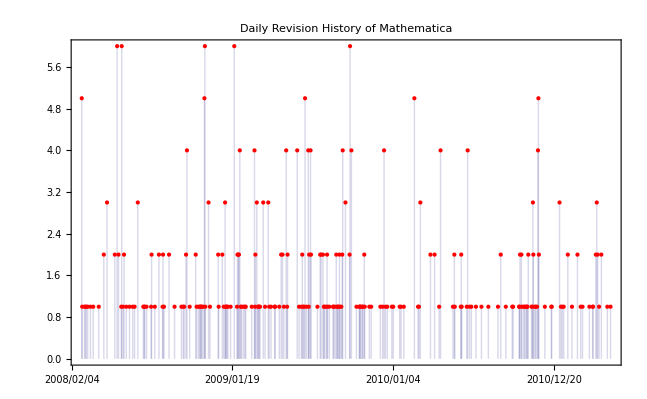

```mathematica
DateListPlot[revhist,PlotStyle->{PointSize[Medium],Red},DateTicksFormat->{"Year","/","Month","/","Day"},Filling->Bottom,AxesOrigin->{Automatic,0},PlotLabel->Style["Daily Revision History of Mathematica",Bold,Large]]
```

```mathematica
mon=Tally[dates[[All,1;;2]]];
```

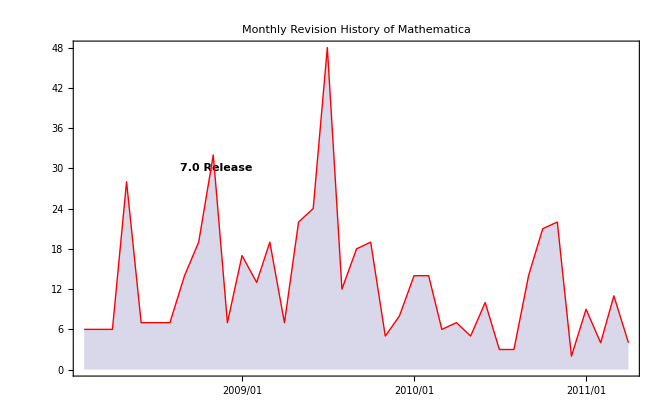

```mathematica
DateListPlot[mon,PlotStyle->{PointSize[Medium],Red},Joined->True,Filling->Bottom,PlotRange->All,DateTicksFormat->{"Year","/","Month"},AxesOrigin->{Automatic,0},PlotLabel->Style["Monthly Revision History of Mathematica",Bold,Large],GridLines->{{{{2008,11,8},Blue}},None},Prolog:>Text[Style["7.0 Release",Medium,Bold],{{2008,11,8},30}]]
```

### Import paged edited by each user

```mathematica
users=data[[All,1]];
```

```mathematica
top5=Sort[Tally[users],#1[[2]]>#2[[2]]&][[1;;5,1]]
```

{Cloudruns,JonMcLoone,Drkirkby,Aldaron,134.206.252.181}

```mathematica
cds=Tally@dates[[Flatten@Position[users,x_/;x==#]]]&/@top5;
Table[cds[[i,All,1]]=Map[AbsoluteTime,cds[[i,All,1]]],{i,5}];
```

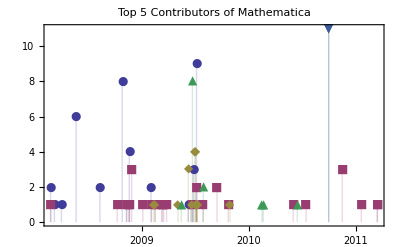

```mathematica
DateListPlot[cds,PlotRange->All,AxesOrigin->{Automatic,0},Filling->Bottom,PlotMarkers->{Automatic,12},PlotLegend->top5,LegendPosition->{0.8,-0.5},LegendShadow->None,PlotLabel->Style["Top 5 Contributors of Mathematica ",Bold,Large]]
```

```mathematica
userpages[usr_]:=Module[{url,uxml,udata,unicase},url="http://en.wikipedia.org/w/api.php?action=query&list=\ 
usercontribs&uclimit=500&format=xml&ucuser="<>usr;
uxml=Import[url,"XML"];
udata=Cases[uxml,XMLElement["item",w_,_]:>w,Infinity];
unicase=DeleteCases[Union["title"/.udata],x_/;(StringMatchQ[x,"User talk:"~~__]||StringMatchQ[x,"Talk:"~~__]||StringMatchQ[x,"User:"~~__])];Map[usr->#&,unicase]];
```

```mathematica
g=userurl[#]&/@top5
```

{{Cloudruns→Ambiguity,Cloudruns→Axiom (computer algebra system),Cloudruns→Charles Greville, 7th Earl of Warwick,Cloudruns→Comparison of computer algebra systems,Cloudruns→Computer cluster,Cloudruns→Edward Walter Hamilton,Cloudruns→File:MathematicaWind.png,Cloudruns→Frank Pakenham, 7th Earl of Longford,Cloudruns→Gavin Henderson, 2nd Baron Faringdon,Cloudruns→Geodesy,Cloudruns→Isabel le Despenser, Countess of Worcester,Cloudruns→List of interactive geometry software,Cloudruns→Mathematica,Cloudruns→Philip Adams,Cloudruns→Richard de Beauchamp, 1st Earl of Worcester,Cloudruns→Sage (mathematics software),Cloudruns→Sir Charles Madden, 1st Baronet,Cloudruns→Template:Computer algebra systems},{JonMcLoone→1940s,JonMcLoone→Absolute value,JonMcLoone→Africville,JonMcLoone→Analytic network process,JonMcLoone→Andrew Dilnot,JonMcLoone→Astrid Lindgren,JonMcLoone→Atreyu (band),JonMcLoone→Auckland,JonMcLoone→AVS Video Editor,JonMcLoone→Bakewell,JonMcLoone→Balrog,JonMcLoone→Barahiya,JonMcLoone→Battlefield Heroes,JonMcLoone→Burwell, Cambridgeshire,JonMcLoone→Butterfly stroke,JonMcLoone→Category:1777 in sports,JonMcLoone→Category:Images with Mathematica source code,JonMcLoone→Centipede,JonMcLoone→Charities Act 2006,JonMcLoone→Charles Marion Russell,JonMcLoone→Cheese on toast,JonMcLoone→Chiviri,JonMcLoone→Civil disobedience,JonMcLoone→Collatz conjecture,JonMcLoone→Colm Imbert,JonMcLoone→Comparison of computer algebra systems,JonMcLoone→Comparison of numerical analysis software,JonMcLoone→Comparison of statistical packages,JonMcLoone→Computational science,JonMcLoone→Condensate pump,JonMcLoone→Correspondence problem,JonMcLoone→Cover Flow,JonMcLoone→C (programming language),JonMcLoone→Creation myth,JonMcLoone→CSV application support,JonMcLoone→Danny Green,JonMcLoone→Daubechies wavelet,JonMcLoone→Deformation theory,JonMcLoone→Differential algebraic equation,JonMcLoone→Doppler effect,JonMcLoone→Dunite,JonMcLoone→Edge detection,JonMcLoone→Elements of art,JonMcLoone→Emotion Engine,JonMcLoone→Estate planning,JonMcLoone→Features new to Windows 7,JonMcLoone→File:Acoustic weighting curves.svg,JonMcLoone→File:Cube root of positive X.png,JonMcLoone→File:Daubechies20LowPassHighPass2DFilterM.png,JonMcLoone→File:EdgeDetectionMathematica.png,JonMcLoone→File:EnumaElish103.jpg,JonMcLoone→File:Frequency.PNG,JonMcLoone→File:Gamma cassiopeiae diagram.jpg,JonMcLoone→File:MathematicaSpikeyVersion8.png,JonMcLoone→File:MathematicaWind.png,JonMcLoone→File:MorinSurfaceCrossView.PNG,JonMcLoone→File:Nonlinear asymptote.svg,JonMcLoone→File:Paraboloid of Revolution.png,JonMcLoone→File:Potential energy well example.png,JonMcLoone→File:Psi cassiopeiae diagram.jpg,JonMcLoone→File:Psi cassiopeiae diagram.pdf,JonMcLoone→File:Simple-manip-mathematica-png.png,JonMcLoone→File:VSVR.png,JonMcLoone→Freesat,JonMcLoone→Freeview (UK),JonMcLoone→Generalized hypergeometric function,JonMcLoone→Geodesy,JonMcLoone→Great Walstead School,JonMcLoone→GridMathematica,JonMcLoone→Grinch,JonMcLoone→Gröbner basis,JonMcLoone→Halftone,JonMcLoone→Integral,JonMcLoone→Interpreted language,JonMcLoone→Inuktitut,JonMcLoone→John M. Clayton,JonMcLoone→Lebanon,JonMcLoone→Linear programming,JonMcLoone→Liquidity risk,JonMcLoone→List of characters in Madagascar (franchise),JonMcLoone→List of digital terrestrial television channels (UK),JonMcLoone→List of file formats,JonMcLoone→List of Ned's Declassified School Survival Guide episodes,JonMcLoone→List of numerical analysis software,JonMcLoone→List of people who have been called "polymaths",JonMcLoone→List of Presidents of Lebanon,JonMcLoone→List of statistical packages,JonMcLoone→List of The Penguins of Madagascar episodes,JonMcLoone→LiveMath,JonMcLoone→Local regression,JonMcLoone→Madagascar (franchise),JonMcLoone→Markov chain,JonMcLoone→Martelle, Iowa,JonMcLoone→Mathematica,JonMcLoone→Mathematical finance,JonMcLoone→Mathematical optimization,JonMcLoone→Matrix (mathematics),JonMcLoone→Modelica,JonMcLoone→Nelder–Mead method,JonMcLoone→Nine-point circle,JonMcLoone→Nobel Prize,JonMcLoone→Norwich City F.C.,JonMcLoone→Numerical analysis,JonMcLoone→Ordinary differential equation,JonMcLoone→Oregon wine,JonMcLoone→Oxfordshire,JonMcLoone→Partial differential equation,JonMcLoone→Pete Finnerty,JonMcLoone→Philadelphia 76ers,JonMcLoone→Probate,JonMcLoone→Publicon,JonMcLoone→QR decomposition,JonMcLoone→Ralph Bunche,JonMcLoone→Rat race,JonMcLoone→Recurrence relation,JonMcLoone→Relative dating,JonMcLoone→Riemann zeta function,JonMcLoone→Robert Peliza,JonMcLoone→Root-finding algorithm,JonMcLoone→Sandstone,JonMcLoone→Security through obscurity,JonMcLoone→Simplex algorithm,JonMcLoone→Simulated annealing,JonMcLoone→Sodium phosphates,JonMcLoone→Solver,JonMcLoone→Sport in Germany,JonMcLoone→St Aidan's College,JonMcLoone→Standing desk,JonMcLoone→Steeple Aston,JonMcLoone→Stephen Wolfram,JonMcLoone→Symbolic integration,JonMcLoone→Template:Latest preview software release/Mathematica,JonMcLoone→Template:Latest stable software release/Mathematica,JonMcLoone→Template:User mathematica-4,JonMcLoone→TeX,JonMcLoone→The Fairly OddParents (season 4),JonMcLoone→The Fairly OddParents (season 7),JonMcLoone→The New Yorker,JonMcLoone→Thick-billed Parrot,JonMcLoone→Timeline of programming languages,JonMcLoone→Trojan Horse,JonMcLoone→Under Armour,JonMcLoone→United States customary units,JonMcLoone→Wallace Givens,JonMcLoone→Wavelet,JonMcLoone→While loop,JonMcLoone→Wikipedia:Articles for deletion/List of numerical analysis software,JonMcLoone→Wikipedia:Categories for discussion/Log/2010 March 6,JonMcLoone→Windows 7,JonMcLoone→Winston Churchill,JonMcLoone→Wolfram Alpha,JonMcLoone→Wolfram Demonstrations Project,JonMcLoone→Wolfram Research},{Drkirkby→Academic degree,Drkirkby→Alekhine's Defence,Drkirkby→Aleksandr Lenderman,Drkirkby→Btrfs,Drkirkby→Catalan Opening,Drkirkby→ChessBase,Drkirkby→Clayton College of Natural Health,Drkirkby→Comparison of computer algebra systems,Drkirkby→Comparison of numerical analysis software,Drkirkby→Comparison of statistical packages,Drkirkby→Computer chess,Drkirkby→Crafty,Drkirkby→Crouch Valley Line,Drkirkby→File:Mathematica-on-iPAQ.jpg,Drkirkby→File:WITM-iPAQ.jpg,Drkirkby→Fritz (chess),Drkirkby→Gillian McKeith,Drkirkby→GridMathematica,Drkirkby→IEEE-488,Drkirkby→Lock-in amplifier,Drkirkby→Maple (software),Drkirkby→Mathematica,Drkirkby→Michelle McManus,Drkirkby→Noise temperature,Drkirkby→Pocket Fritz,Drkirkby→Print on demand,Drkirkby→Publicon,Drkirkby→Sage (mathematics software),Drkirkby→Shane's Chess Information Database,Drkirkby→Step recovery diode,Drkirkby→Subatomic particle,Drkirkby→Ultra 80,Drkirkby→Ultra Fractal,Drkirkby→Unix,Drkirkby→Usage share of web browsers,Drkirkby→W3C Markup Validation Service,Drkirkby→Wikipedia:Articles for deletion/ChessDB,Drkirkby→Wikipedia:Articles for deletion/Geoffrey Borg,Drkirkby→Wikipedia:Articles for deletion/Log/2009 May 15,Drkirkby→Wikipedia:Articles for deletion/Publicon,Drkirkby→Wikipedia:Articles for deletion/Pure (programming language),Drkirkby→Wikipedia:Articles for deletion/Pure (programming language) (2nd nomination),Drkirkby→Wikipedia:Conflict of interest/Noticeboard,Drkirkby→Wikipedia:Help desk,Drkirkby→Wikipedia:Media copyright questions,Drkirkby→Wikipedia:Sandbox/Archive,Drkirkby→Wolfram Alpha,Drkirkby→Xeon,Drkirkby→Yagi-Uda antenna},{Aldaron→Abstract strategy game,Aldaron→Anathem,Aldaron→Ancient Rome,Aldaron→Anita Bryant,Aldaron→Balance of Power (video game),Aldaron→Biathlon,Aldaron→BoardGameGeek,Aldaron→Carcassonne (board game),Aldaron→Chatroulette,Aldaron→Christian,Aldaron→Christian Nadé,Aldaron→Collectible card game,Aldaron→Constellation,Aldaron→COROT,Aldaron→COROT-9b,Aldaron→COROT-Exo-9b,Aldaron→Cosmic Wimpout,Aldaron→Criticism of patents,Aldaron→Cthulhu,Aldaron→Discoveries of extrasolar planets,Aldaron→Doppler effect,Aldaron→Doppler spectroscopy,Aldaron→Extrasolar planet,Aldaron→Extraterrestrial life,Aldaron→Extraterrestrial skies,Aldaron→File:Care Bears.png,Aldaron→Gas giant,Aldaron→GIPF project,Aldaron→Gliese,Aldaron→Gliese 581,Aldaron→Gliese 581 c,Aldaron→Gliese 581 e,Aldaron→Gliese 581 g,Aldaron→Global Ideas Bank,Aldaron→Gold's Gym,Aldaron→GRB 090423,Aldaron→Greek astronomy,Aldaron→HD 136418 b,Aldaron→HD 180902 b,Aldaron→HD 181342 b,Aldaron→HD 206610 b,Aldaron→HD 212771 b,Aldaron→HD 24496 Ab,Aldaron→HD 4313 b,Aldaron→HD 95089 b,Aldaron→Hot Jupiter,Aldaron→HR 8799 b,Aldaron→HR 8799 c,Aldaron→HR 8799 d,Aldaron→Hubble Space Telescope,Aldaron→Iapetus (moon),Aldaron→Idea,Aldaron→Ideas bank,Aldaron→Invention,Aldaron→Isles of Shoals,Aldaron→Jack Russell Terrier,Aldaron→James Taylor,Aldaron→Jerome H. Lemelson,Aldaron→Johannes Kepler,Aldaron→KenKen,Aldaron→Kepler-10,Aldaron→Kepler-10 b,Aldaron→Kepler-10b,Aldaron→Kepler-10 c,Aldaron→Kepler-4,Aldaron→Kepler-5,Aldaron→Kepler-6,Aldaron→Kepler-8,Aldaron→Kepler-9,Aldaron→Kepler-9 b,Aldaron→Kepler-9b,Aldaron→Kepler-9 c,Aldaron→Kepler-9c,Aldaron→Kepler (spacecraft),Aldaron→KOI-377.03,Aldaron→KOI-72.02,Aldaron→Liquid nitrogen,Aldaron→List of planetary systems,Aldaron→Lyra,Aldaron→Maternal insult,Aldaron→Mathematica,Aldaron→McLean Hospital,Aldaron→Miguel A. Núñez, Jr.,Aldaron→Nutrition,Aldaron→Objective-C,Aldaron→Ocean planet,Aldaron→Parsec,Aldaron→Pete Bethune,Aldaron→Philip Glass,Aldaron→Planet,Aldaron→PSR B1257+12 A,Aldaron→Ronald McDonald,Aldaron→Shinto,Aldaron→Shoe,Aldaron→Slash (musician),Aldaron→Solar flare,Aldaron→Starry Night (planetarium software),Aldaron→Sudarsky extrasolar planet classification,Aldaron→Super-Earth,Aldaron→Television,Aldaron→Template:Kepler-10,Aldaron→Template:Kepler-9,Aldaron→Template:User page,Aldaron→Template:User US Patents Filed,Aldaron→Template:User US Patents Issued,Aldaron→Tom Welling,Aldaron→Transylvania,Aldaron→Universe,Aldaron→Ursa Minor,Aldaron→Wandsworth (HM Prison),Aldaron→WASP-12b,Aldaron→WASP-8b,Aldaron→Wheaton College,Aldaron→Wheaton College (Massachusetts),Aldaron→Wikipedia:Administrator intervention against vandalism,Aldaron→Wikipedia:Articles for deletion/Hot companion,Aldaron→Wikipedia talk:WikiProject Astronomical objects,Aldaron→Wikipedia:WikiProject Military history/Strategy/News and editorials/Delivery options,Aldaron→Wolfgang Amadeus Mozart,Aldaron→World War II casualties},{134.206.252.181→Mathematica}}

```mathematica
gp=Flatten[g,1]
```

{Cloudruns→Ambiguity,Cloudruns→Axiom (computer algebra system),Cloudruns→Charles Greville, 7th Earl of Warwick,Cloudruns→Comparison of computer algebra systems,Cloudruns→Computer cluster,Cloudruns→Edward Walter Hamilton,Cloudruns→File:MathematicaWind.png,Cloudruns→Frank Pakenham, 7th Earl of Longford,Cloudruns→Gavin Henderson, 2nd Baron Faringdon,Cloudruns→Geodesy,Cloudruns→Isabel le Despenser, Countess of Worcester,Cloudruns→List of interactive geometry software,Cloudruns→Mathematica,Cloudruns→Philip Adams,Cloudruns→Richard de Beauchamp, 1st Earl of Worcester,Cloudruns→Sage (mathematics software),Cloudruns→Sir Charles Madden, 1st Baronet,Cloudruns→Template:Computer algebra systems,JonMcLoone→1940s,JonMcLoone→Absolute value,JonMcLoone→Africville,JonMcLoone→Analytic network process,JonMcLoone→Andrew Dilnot,JonMcLoone→Astrid Lindgren,JonMcLoone→Atreyu (band),JonMcLoone→Auckland,JonMcLoone→AVS Video Editor,JonMcLoone→Bakewell,JonMcLoone→Balrog,JonMcLoone→Barahiya,JonMcLoone→Battlefield Heroes,JonMcLoone→Burwell, Cambridgeshire,JonMcLoone→Butterfly stroke,JonMcLoone→Category:1777 in sports,JonMcLoone→Category:Images with Mathematica source code,JonMcLoone→Centipede,JonMcLoone→Charities Act 2006,JonMcLoone→Charles Marion Russell,JonMcLoone→Cheese on toast,JonMcLoone→Chiviri,JonMcLoone→Civil disobedience,JonMcLoone→Collatz conjecture,JonMcLoone→Colm Imbert,JonMcLoone→Comparison of computer algebra systems,JonMcLoone→Comparison of numerical analysis software,JonMcLoone→Comparison of statistical packages,JonMcLoone→Computational science,JonMcLoone→Condensate pump,JonMcLoone→Correspondence problem,JonMcLoone→Cover Flow,JonMcLoone→C (programming language),JonMcLoone→Creation myth,JonMcLoone→CSV application support,JonMcLoone→Danny Green,JonMcLoone→Daubechies wavelet,JonMcLoone→Deformation theory,JonMcLoone→Differential algebraic equation,JonMcLoone→Doppler effect,JonMcLoone→Dunite,JonMcLoone→Edge detection,JonMcLoone→Elements of art,JonMcLoone→Emotion Engine,JonMcLoone→Estate planning,JonMcLoone→Features new to Windows 7,JonMcLoone→File:Acoustic weighting curves.svg,JonMcLoone→File:Cube root of positive X.png,JonMcLoone→File:Daubechies20LowPassHighPass2DFilterM.png,JonMcLoone→File:EdgeDetectionMathematica.png,JonMcLoone→File:EnumaElish103.jpg,JonMcLoone→File:Frequency.PNG,JonMcLoone→File:Gamma cassiopeiae diagram.jpg,JonMcLoone→File:MathematicaSpikeyVersion8.png,JonMcLoone→File:MathematicaWind.png,JonMcLoone→File:MorinSurfaceCrossView.PNG,JonMcLoone→File:Nonlinear asymptote.svg,JonMcLoone→File:Paraboloid of Revolution.png,JonMcLoone→File:Potential energy well example.png,JonMcLoone→File:Psi cassiopeiae diagram.jpg,JonMcLoone→File:Psi cassiopeiae diagram.pdf,JonMcLoone→File:Simple-manip-mathematica-png.png,JonMcLoone→File:VSVR.png,JonMcLoone→Freesat,JonMcLoone→Freeview (UK),JonMcLoone→Generalized hypergeometric function,JonMcLoone→Geodesy,JonMcLoone→Great Walstead School,JonMcLoone→GridMathematica,JonMcLoone→Grinch,JonMcLoone→Gröbner basis,JonMcLoone→Halftone,JonMcLoone→Integral,JonMcLoone→Interpreted language,JonMcLoone→Inuktitut,JonMcLoone→John M. Clayton,JonMcLoone→Lebanon,JonMcLoone→Linear programming,JonMcLoone→Liquidity risk,JonMcLoone→List of characters in Madagascar (franchise),JonMcLoone→List of digital terrestrial television channels (UK),JonMcLoone→List of file formats,JonMcLoone→List of Ned's Declassified School Survival Guide episodes,JonMcLoone→List of numerical analysis software,JonMcLoone→List of people who have been called "polymaths",JonMcLoone→List of Presidents of Lebanon,JonMcLoone→List of statistical packages,JonMcLoone→List of The Penguins of Madagascar episodes,JonMcLoone→LiveMath,JonMcLoone→Local regression,JonMcLoone→Madagascar (franchise),JonMcLoone→Markov chain,JonMcLoone→Martelle, Iowa,JonMcLoone→Mathematica,JonMcLoone→Mathematical finance,JonMcLoone→Mathematical optimization,JonMcLoone→Matrix (mathematics),JonMcLoone→Modelica,JonMcLoone→Nelder–Mead method,JonMcLoone→Nine-point circle,JonMcLoone→Nobel Prize,JonMcLoone→Norwich City F.C.,JonMcLoone→Numerical analysis,JonMcLoone→Ordinary differential equation,JonMcLoone→Oregon wine,JonMcLoone→Oxfordshire,JonMcLoone→Partial differential equation,JonMcLoone→Pete Finnerty,JonMcLoone→Philadelphia 76ers,JonMcLoone→Probate,JonMcLoone→Publicon,JonMcLoone→QR decomposition,JonMcLoone→Ralph Bunche,JonMcLoone→Rat race,JonMcLoone→Recurrence relation,JonMcLoone→Relative dating,JonMcLoone→Riemann zeta function,JonMcLoone→Robert Peliza,JonMcLoone→Root-finding algorithm,JonMcLoone→Sandstone,JonMcLoone→Security through obscurity,JonMcLoone→Simplex algorithm,JonMcLoone→Simulated annealing,JonMcLoone→Sodium phosphates,JonMcLoone→Solver,JonMcLoone→Sport in Germany,JonMcLoone→St Aidan's College,JonMcLoone→Standing desk,JonMcLoone→Steeple Aston,JonMcLoone→Stephen Wolfram,JonMcLoone→Symbolic integration,JonMcLoone→Template:Latest preview software release/Mathematica,JonMcLoone→Template:Latest stable software release/Mathematica,JonMcLoone→Template:User mathematica-4,JonMcLoone→TeX,JonMcLoone→The Fairly OddParents (season 4),JonMcLoone→The Fairly OddParents (season 7),JonMcLoone→The New Yorker,JonMcLoone→Thick-billed Parrot,JonMcLoone→Timeline of programming languages,JonMcLoone→Trojan Horse,JonMcLoone→Under Armour,JonMcLoone→United States customary units,JonMcLoone→Wallace Givens,JonMcLoone→Wavelet,JonMcLoone→While loop,JonMcLoone→Wikipedia:Articles for deletion/List of numerical analysis software,JonMcLoone→Wikipedia:Categories for discussion/Log/2010 March 6,JonMcLoone→Windows 7,JonMcLoone→Winston Churchill,JonMcLoone→Wolfram Alpha,JonMcLoone→Wolfram Demonstrations Project,JonMcLoone→Wolfram Research,Drkirkby→Academic degree,Drkirkby→Alekhine's Defence,Drkirkby→Aleksandr Lenderman,Drkirkby→Btrfs,Drkirkby→Catalan Opening,Drkirkby→ChessBase,Drkirkby→Clayton College of Natural Health,Drkirkby→Comparison of computer algebra systems,Drkirkby→Comparison of numerical analysis software,Drkirkby→Comparison of statistical packages,Drkirkby→Computer chess,Drkirkby→Crafty,Drkirkby→Crouch Valley Line,Drkirkby→File:Mathematica-on-iPAQ.jpg,Drkirkby→File:WITM-iPAQ.jpg,Drkirkby→Fritz (chess),Drkirkby→Gillian McKeith,Drkirkby→GridMathematica,Drkirkby→IEEE-488,Drkirkby→Lock-in amplifier,Drkirkby→Maple (software),Drkirkby→Mathematica,Drkirkby→Michelle McManus,Drkirkby→Noise temperature,Drkirkby→Pocket Fritz,Drkirkby→Print on demand,Drkirkby→Publicon,Drkirkby→Sage (mathematics software),Drkirkby→Shane's Chess Information Database,Drkirkby→Step recovery diode,Drkirkby→Subatomic particle,Drkirkby→Ultra 80,Drkirkby→Ultra Fractal,Drkirkby→Unix,Drkirkby→Usage share of web browsers,Drkirkby→W3C Markup Validation Service,Drkirkby→Wikipedia:Articles for deletion/ChessDB,Drkirkby→Wikipedia:Articles for deletion/Geoffrey Borg,Drkirkby→Wikipedia:Articles for deletion/Log/2009 May 15,Drkirkby→Wikipedia:Articles for deletion/Publicon,Drkirkby→Wikipedia:Articles for deletion/Pure (programming language),Drkirkby→Wikipedia:Articles for deletion/Pure (programming language) (2nd nomination),Drkirkby→Wikipedia:Conflict of interest/Noticeboard,Drkirkby→Wikipedia:Help desk,Drkirkby→Wikipedia:Media copyright questions,Drkirkby→Wikipedia:Sandbox/Archive,Drkirkby→Wolfram Alpha,Drkirkby→Xeon,Drkirkby→Yagi-Uda antenna,Aldaron→Abstract strategy game,Aldaron→Anathem,Aldaron→Ancient Rome,Aldaron→Anita Bryant,Aldaron→Balance of Power (video game),Aldaron→Biathlon,Aldaron→BoardGameGeek,Aldaron→Carcassonne (board game),Aldaron→Chatroulette,Aldaron→Christian,Aldaron→Christian Nadé,Aldaron→Collectible card game,Aldaron→Constellation,Aldaron→COROT,Aldaron→COROT-9b,Aldaron→COROT-Exo-9b,Aldaron→Cosmic Wimpout,Aldaron→Criticism of patents,Aldaron→Cthulhu,Aldaron→Discoveries of extrasolar planets,Aldaron→Doppler effect,Aldaron→Doppler spectroscopy,Aldaron→Extrasolar planet,Aldaron→Extraterrestrial life,Aldaron→Extraterrestrial skies,Aldaron→File:Care Bears.png,Aldaron→Gas giant,Aldaron→GIPF project,Aldaron→Gliese,Aldaron→Gliese 581,Aldaron→Gliese 581 c,Aldaron→Gliese 581 e,Aldaron→Gliese 581 g,Aldaron→Global Ideas Bank,Aldaron→Gold's Gym,Aldaron→GRB 090423,Aldaron→Greek astronomy,Aldaron→HD 136418 b,Aldaron→HD 180902 b,Aldaron→HD 181342 b,Aldaron→HD 206610 b,Aldaron→HD 212771 b,Aldaron→HD 24496 Ab,Aldaron→HD 4313 b,Aldaron→HD 95089 b,Aldaron→Hot Jupiter,Aldaron→HR 8799 b,Aldaron→HR 8799 c,Aldaron→HR 8799 d,Aldaron→Hubble Space Telescope,Aldaron→Iapetus (moon),Aldaron→Idea,Aldaron→Ideas bank,Aldaron→Invention,Aldaron→Isles of Shoals,Aldaron→Jack Russell Terrier,Aldaron→James Taylor,Aldaron→Jerome H. Lemelson,Aldaron→Johannes Kepler,Aldaron→KenKen,Aldaron→Kepler-10,Aldaron→Kepler-10 b,Aldaron→Kepler-10b,Aldaron→Kepler-10 c,Aldaron→Kepler-4,Aldaron→Kepler-5,Aldaron→Kepler-6,Aldaron→Kepler-8,Aldaron→Kepler-9,Aldaron→Kepler-9 b,Aldaron→Kepler-9b,Aldaron→Kepler-9 c,Aldaron→Kepler-9c,Aldaron→Kepler (spacecraft),Aldaron→KOI-377.03,Aldaron→KOI-72.02,Aldaron→Liquid nitrogen,Aldaron→List of planetary systems,Aldaron→Lyra,Aldaron→Maternal insult,Aldaron→Mathematica,Aldaron→McLean Hospital,Aldaron→Miguel A. Núñez, Jr.,Aldaron→Nutrition,Aldaron→Objective-C,Aldaron→Ocean planet,Aldaron→Parsec,Aldaron→Pete Bethune,Aldaron→Philip Glass,Aldaron→Planet,Aldaron→PSR B1257+12 A,Aldaron→Ronald McDonald,Aldaron→Shinto,Aldaron→Shoe,Aldaron→Slash (musician),Aldaron→Solar flare,Aldaron→Starry Night (planetarium software),Aldaron→Sudarsky extrasolar planet classification,Aldaron→Super-Earth,Aldaron→Television,Aldaron→Template:Kepler-10,Aldaron→Template:Kepler-9,Aldaron→Template:User page,Aldaron→Template:User US Patents Filed,Aldaron→Template:User US Patents Issued,Aldaron→Tom Welling,Aldaron→Transylvania,Aldaron→Universe,Aldaron→Ursa Minor,Aldaron→Wandsworth (HM Prison),Aldaron→WASP-12b,Aldaron→WASP-8b,Aldaron→Wheaton College,Aldaron→Wheaton College (Massachusetts),Aldaron→Wikipedia:Administrator intervention against vandalism,Aldaron→Wikipedia:Articles for deletion/Hot companion,Aldaron→Wikipedia talk:WikiProject Astronomical objects,Aldaron→Wikipedia:WikiProject Military history/Strategy/News and editorials/Delivery options,Aldaron→Wolfgang Amadeus Mozart,Aldaron→World War II casualties,134.206.252.181→Mathematica}

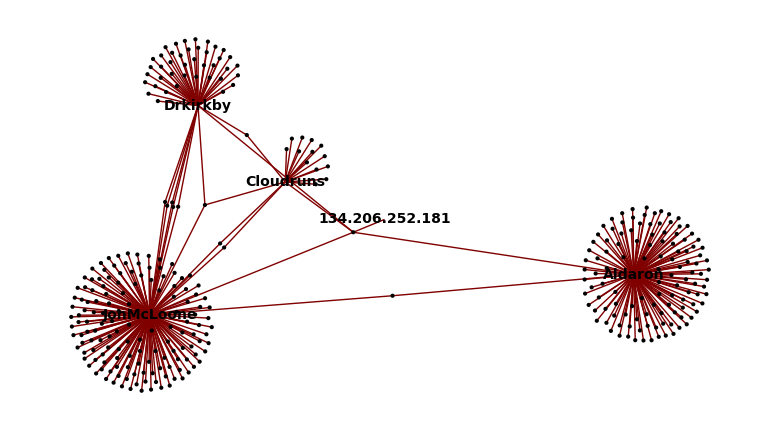

```mathematica
GraphPlot[gp,VertexRenderingFunction->(If[MemberQ[top5,#2],Text[Style[#2,Bold,14],#1,Background->LightYellow],Blue;Point[#1]]&)]
```

```mathematica
commons=Select[Tally[gp[[All,2]]],#[[2]]>=2&][[All,1]];
```

```mathematica
commongp=Select[gp,MemberQ[commons,#[[2]]]&];
```

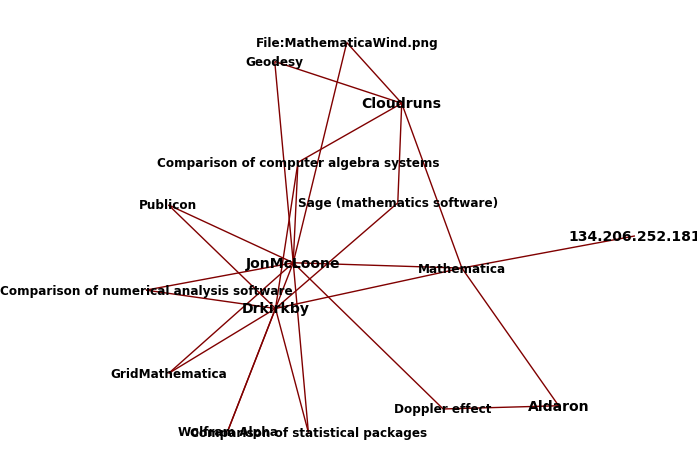

```mathematica
GraphPlot[commongp,VertexRenderingFunction->(If[MemberQ[top5,#2],Text[Style[#2,Bold,14],#1,Background->LightYellow],Text[Style[#2,Bold,12],#1,Background->LightBlue]]&)]
```